```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
Off[Needs::nocont];Needs["LowDiscrep`"];
On[Needs::nocont];
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Geometry

We consider a 1D geometry [0,1] and consider all pairs within δ of one another.

```mathematica
(* Distance function between two pairs *)
```

```mathematica
Clear[distFunc]; Clear[distFuncC];
distFunc[x_List, δ_:0.2]:= If[Abs[x[[1]]-x[[2]]] < δ, 1.0, 0.0];
distFuncC[δ_]:=distFuncC[δ]=Module[{},Compile[{{x,_Real,1}},
If[Abs[x[[1]]-x[[2]]] < δ, 1.0, 0.0], 
CompilationTarget->"C", 
RuntimeAttributes->{Listable}, 
Parallelization->True]];
```

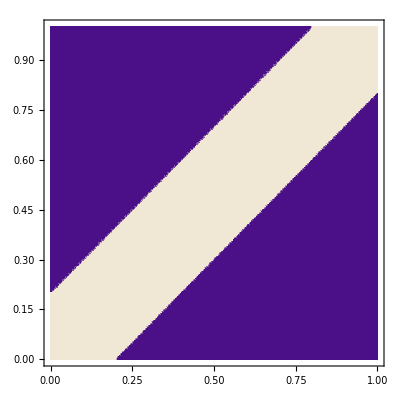

```mathematica
(* Plot this function *)
DensityPlot[distFunc[{x,y}], {x, 0,1}, {y, 0, 1}, PlotPoints->100]
```

```mathematica
(* Define analytic RR *)
analyticRR[δ_:0.2] := NIntegrate[distFunc[{x,y}],{x,0,1},{y,0,1}];
```

```mathematica
analyticRR[]
```

0.36

## Timing DistFunc

```mathematica
Timing[distFunc[#, 0.2]& /@ generateRandomGrid[1000,1];]
```

{13.2403,Null}

```mathematica
Timing[distFuncC[0.2][generateRandomGrid[1000,1]];]
```

{1.44013,Null}

```mathematica
Timing[distFuncC[0.2]/@ generateRandomGrid[1000,1];]
```

{1.09087,Null}

```mathematica
test1 = generateRandomGrid[100,1];
```

```mathematica
distFuncC[0.2][test1] == (distFunc[#, 0.2] & /@ test1)
```

True

## Random vs LDS grids

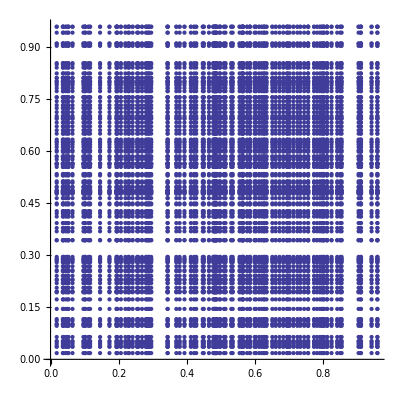

```mathematica
ListPlot[generateRandomGrid[100], AspectRatio->1]
```

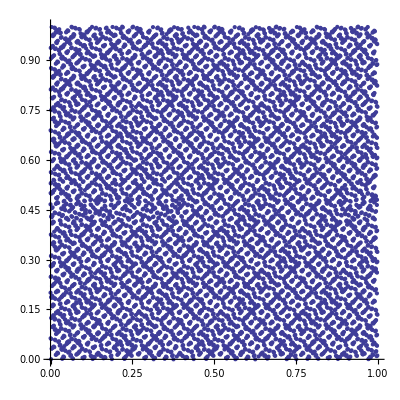

```mathematica
ListPlot[generateLDSshiftedGrid[100^2], AspectRatio->1]
```

## Simple Monte Carlo Integration

Start by comparing errors for 100^2points.

```mathematica
Timing[v1 = Reap[Do[Sow[mcIntegrate[distFuncC[0.2], generateRandomGrid[100, 1]]],{10000}]][[2,1]];]
```

{95.9203,Null}

```mathematica
Timing[v2 =Reap[Do[Sow[mcIntegrate[distFuncC[0.2], generateLDSshiftedGrid[100^2,2]]], {10000}]][[2,1]];]
```

{38.1487,Null}

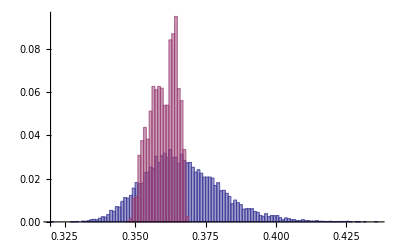

```mathematica
Histogram[{v1, v2}, {0.001}, "Probability"]
```

```mathematica
rootnvals = {10,40, 160, 640};
nvals = rootnvals^2;
```

```mathematica
Timing[ran1 = Table[getmeanerror[mcIntegrate[distFuncC[0.2], generateRandomGrid[ii,1]], 1000], {ii, rootnvals}]/analyticRR[];]
```

{456.27,Null}

```mathematica
ran1
```

{{1.18233,0.20204},{1.04608,0.0682715},{1.01038,0.0284293},{1.00326,0.0140005}}

```mathematica
Timing[lds1=Table[getmeanerror[mcIntegrate[distFuncC[0.2], generateLDSshiftedGrid[ii,2]], 1000], {ii, nvals}]/analyticRR[];]
```

{165.529,Null}

```mathematica
lds1
```

{{0.995778,0.0972665},{1.00039,0.0213056},{0.999862,0.00381408},{1.00003,0.000569331}}

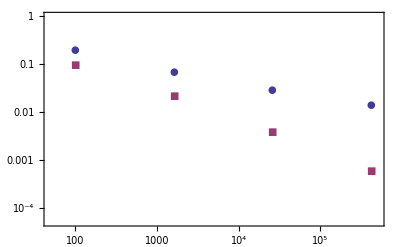

```mathematica
ListLogLogPlot[{Transpose[{nvals, ran1[[All,2]]}], Transpose[{nvals, lds1[[All, 2]]}]}, Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{{50, 500000}, {5.*^-5, 1}}]
```

## Change variables to improve convergence

```mathematica
Clear[distFunc2];
Clear[distFunc2C];
distFunc2[x_List, δ_:0.2]:= With[{x1 =x[[1]]+2δ x[[1]] - δ}, 
If[(x1>0) && (x1 < 1), 1.0, 0.0]*2δ
];
distFunc2C[δ_]:=distFunc2C[δ] = Module[{},Compile[{{x,_Real,1}},
With[ {x1 =x[[1]]+2 δ x[[2]]- δ}, 
2δ If[(x1>0) && (x1 < 1), 1.0, 0.0]], 
CompilationTarget->"C", RuntimeAttributes->{Listable}]];
```

```mathematica
Timing[distFunc2 /@ generateLDSshiftedGrid[1000^2,2];]
```

{20.211,Null}

```mathematica
Timing[distFunc2C[0.2][generateLDSshiftedGrid[1000^2,2]];]
```

{0.426866,Null}

```mathematica
Timing[lds2=Table[getmeanerror[mcIntegrate[distFunc2C[0.2], generateLDSshiftedGrid[ii,2]], 1000], {ii, nvals}]/analyticRR[];]
```

{161.195,Null}

```mathematica
lds2
```

{{1.0003,0.0199738},{0.999996,0.00258216},{0.99999,0.000293444},{1.,0.0000272077}}

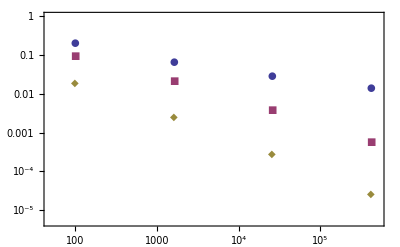

```mathematica
ListLogLogPlot[{Transpose[{nvals, ran1[[All,2]]}], Transpose[{nvals, lds1[[All, 2]]}],Transpose[{nvals, lds2[[All, 2]]}]}, 
Frame->True, 
PlotMarkers->{Automatic, 10}, 
PlotRange->{{50, 500000}, {5.*^-6, 1}}]
```